# Midterm 2

Note 1: If you get to a part where you know exactly what you need to do but don’t know how to make Mathematica do it, please write clearly and explicitly what you would do. We will give you at least partial credit for correct reasoning even if the code doesn’t quite work. (But do your best to get the code to work! All Mathematica techniques you will need for this exam you have already seen in some form in the homework.)

Note 2: For these Mathematica problems, if you do some work on a separate piece of paper and want to submit it for possible partial credit, please append it to your written submissions and clearly indicate which problem your work corresponds to. If your work is not neat enough to be deciphered reasonably easily, it will be difficult for us to award partial credit.

## Problem 4

```mathematica
Quit[]
```

Two identical charged particles are constrained to move on the surface of a sphere without friction and in the absence of any gravitational force (although the Coulomb force is still present). The particles are placed at the positions shown below and released from rest. The azimuthal angle for both particles is initially zero.

-Graphics-

Part A: Give a brief qualitative description of the motion of the system after the particles are released. In particular, describe how the polar angle of each particle (i.e., the angle from the z axis) evolves with time and how the azimuthal angle of each particle evolves with time. If you would like to draw a sketch to help with your description, you may include that with the written portion of the exam that you submit. Just let us know that we should look for it.

Your answer here: 
There will be no motion in the azimuthal direction because the forces on the charged particles will not cause motion in that direction. But there will be motion in the polar direction where the charged particles will oscillate between their min and max positions.

Part B: Using the generalized coordinates th1, phi1, th2, and phi2 corresponding to the spherical angles of the two particles, respectively, determine the Lagrangian for the system. You need not worry about simplifying anything. Feel free to write things down in terms of Cartesian coordinates and their time derivatives if you prefer, but be sure to express those Cartesian coordinates and their derivatives in terms of your generalized coordinates.

Note 1: Let the mass of each particle be m, the radius of the sphere be R, and the charge of each particle be q. We will plug in values for these quantities later, so just leave them symbolic for now.
Note 2: Recall that the Coulomb potential energy for two charges is U = k q1 q2 / r, where r is the distance between the two particles.

```mathematica
(* fill in any preliminary code here *)

(*Cartesian coordinates of first particle*)
x1 = R*Sin[th1]*Cos[phi1];
y1 = R*Sin[th1]*Sin[phi1];
z1 = R*Cos[th1];
(*Cartesian coordinates of second particle*)
x2 =R*Sin[th2]*Cos[phi2];
y2=R*Sin[th2]*Sin[phi2];
z2 =R*Cos[th2];
(*total distance between two particles*)
r = Sqrt[(x1 - x2)^2 + (y1 -y2)^2 +(z1 - z2)^2]
(*KE*)
T = m*(th1dot^2 + phi1dot^2)/2 + m*(th2dot^2 + phi2dot^2)/2
(*PE*)
U=k*q^2/r
(*Lagrangian*)
L=T-U
```

√((R Cos[th1]-R Cos[th2])^2+(R Cos[phi1] Sin[th1]-R Cos[phi2] Sin[th2])^2+(R Sin[phi1] Sin[th1]-R Sin[phi2] Sin[th2])^2)

1/2 m (phi1dot^2+th1dot^2)+1/2 m (phi2dot^2+th2dot^2)

(k q^2)/(√((R Cos[th1]-R Cos[th2])^2+(R Cos[phi1] Sin[th1]-R Cos[phi2] Sin[th2])^2+(R Sin[phi1] Sin[th1]-R Sin[phi2] Sin[th2])^2))

1/2 m (phi1dot^2+th1dot^2)+1/2 m (phi2dot^2+th2dot^2)-(k q^2)/(√((R Cos[th1]-R Cos[th2])^2+(R Cos[phi1] Sin[th1]-R Cos[phi2] Sin[th2])^2+(R Sin[phi1] Sin[th1]-R Sin[phi2] Sin[th2])^2))

Part C: Set up the equations of motion. I have provided the replacement rule to insert the explicit time dependence and values for the following relevant quantities:
m = 0.1 kg
R = 1.0 meter
k = 1.0 (let’s pretend we are in a different universe where the electrostatic constant has this value!)
q = 1.0 Coulomb

Note: These equations will likely look super nasty, and that’s okay!

```mathematica
rule={th1->th1[t],th1dot->th1'[t],phi1->phi1[t],phi1dot->phi1'[t],th2->th2[t],th2dot->th2'[t],phi2->phi2[t],phi2dot->phi2'[t],m->0.1,R->1.0,k->1.0,q->1.0};

(*Derivatives for first particle*)
(*th1*)
dLdth1=D[L,th1]/.rule;
dLdth1dot = D[L, th1dot]/.rule;
(*phi1*)
dLdphi1 = D[L, phi1]/.rule;
dLdphi1dot = D[L, phi1dot]/.rule;

(*Derivatives for second particle*)
(*th2*)
dLdth2 = D[L, th2]/.rule;
dLdth2dot = D[L, th2dot]/.rule;
(*phi2*)
dLdphi2 = D[L, phi2]/.rule;
dLdphi2dot = D[L, phi2dot]/.rule;

(*Euler-Lagrange equations*)
(*th1*)
eqth1=dLdth1==D[dLdth1dot, t]
(*phi1*)
eqphi1=dLdphi1==D[dLdphi1dot, t]
(*th2*)
eqth2=dLdth2==D[dLdth2dot, t]
eqphi2=dLdphi2==D[dLdphi2dot, t]
```

(0.5 (-2. (1. Cos[th1[t]]-1. Cos[th2[t]]) Sin[th1[t]]+2. Cos[phi1[t]] Cos[th1[t]] (1. Cos[phi1[t]] Sin[th1[t]]-1. Cos[phi2[t]] Sin[th2[t]])+2. Cos[th1[t]] Sin[phi1[t]] (1. Sin[phi1[t]] Sin[th1[t]]-1. Sin[phi2[t]] Sin[th2[t]])))/((1. Cos[th1[t]]-1. Cos[th2[t]])^2+(1. Cos[phi1[t]] Sin[th1[t]]-1. Cos[phi2[t]] Sin[th2[t]])^2+(1. Sin[phi1[t]] Sin[th1[t]]-1. Sin[phi2[t]] Sin[th2[t]])^2)^(3/2)==0.1 th1''[t]

(0.5 (-2. Sin[phi1[t]] Sin[th1[t]] (1. Cos[phi1[t]] Sin[th1[t]]-1. Cos[phi2[t]] Sin[th2[t]])+2. Cos[phi1[t]] Sin[th1[t]] (1. Sin[phi1[t]] Sin[th1[t]]-1. Sin[phi2[t]] Sin[th2[t]])))/((1. Cos[th1[t]]-1. Cos[th2[t]])^2+(1. Cos[phi1[t]] Sin[th1[t]]-1. Cos[phi2[t]] Sin[th2[t]])^2+(1. Sin[phi1[t]] Sin[th1[t]]-1. Sin[phi2[t]] Sin[th2[t]])^2)^(3/2)==0.1 phi1''[t]

(0.5 (2. (1. Cos[th1[t]]-1. Cos[th2[t]]) Sin[th2[t]]-2. Cos[phi2[t]] Cos[th2[t]] (1. Cos[phi1[t]] Sin[th1[t]]-1. Cos[phi2[t]] Sin[th2[t]])-2. Cos[th2[t]] Sin[phi2[t]] (1. Sin[phi1[t]] Sin[th1[t]]-1. Sin[phi2[t]] Sin[th2[t]])))/((1. Cos[th1[t]]-1. Cos[th2[t]])^2+(1. Cos[phi1[t]] Sin[th1[t]]-1. Cos[phi2[t]] Sin[th2[t]])^2+(1. Sin[phi1[t]] Sin[th1[t]]-1. Sin[phi2[t]] Sin[th2[t]])^2)^(3/2)==0.1 th2''[t]

(0.5 (2. Sin[phi2[t]] Sin[th2[t]] (1. Cos[phi1[t]] Sin[th1[t]]-1. Cos[phi2[t]] Sin[th2[t]])-2. Cos[phi2[t]] Sin[th2[t]] (1. Sin[phi1[t]] Sin[th1[t]]-1. Sin[phi2[t]] Sin[th2[t]])))/((1. Cos[th1[t]]-1. Cos[th2[t]])^2+(1. Cos[phi1[t]] Sin[th1[t]]-1. Cos[phi2[t]] Sin[th2[t]])^2+(1. Sin[phi1[t]] Sin[th1[t]]-1. Sin[phi2[t]] Sin[th2[t]])^2)^(3/2)==0.1 phi2''[t]

Part D: Using the initial conditions described at the beginning of the problem, solve the differential equations for the first 10 seconds and plot the time evolution of the generalized coordinates. Hopefully this will be consistent with your qualitative description given earlier. Estimate the period of the motion to the nearest tenth of a second.

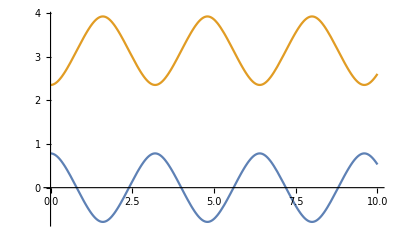

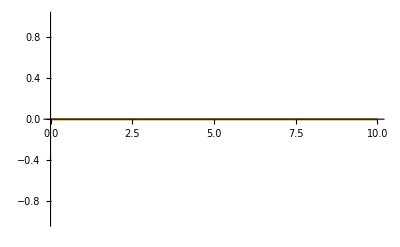

```mathematica
bc={th1[0]==Pi/4, th1'[0]==0, phi1[0]==0, phi1'[0]==0, th2[0]==3*Pi/4, th2'[0]==0, phi2[0]==0, phi2'[0]==0};

sol1=NDSolve[{eqth1,eqphi1,eqth2,eqphi2,bc},{th1,phi1,th2,phi2},{t,0,10}];

Plot[{th1[t]/.sol1,th2[t]/.sol1},{t,0,10}] 
Plot[{phi1[t]/.sol1,phi2[t]/.sol1},{t,0,10}]
```

Period of the motion to the nearest tenth of a second: 
3.2 Seconds

Part E: Both particles are now placed at a polar angle of Pi/2, but their azimuthal angles phi1 and phi2 are allowed to be different. Using physical reasoning, come up with a set of initial azimuthal angles that will result in no motion of the system whatsoever once it is released from rest. Solve the equations for these new initial conditions and demonstrate that no motion occurs.

Note: When solving the differential equations numerically, there may be extremely small variations of the coordinates as a function of time. Check the y-axis scale to verify that any variation you see is very small.

-Graphics-

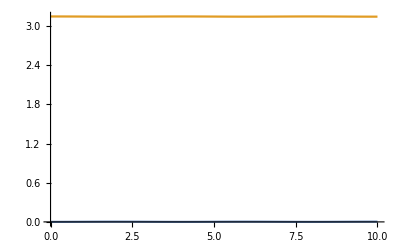

```mathematica
bc2={th1[0]==Pi/2, th1'[0]==0, phi1[0]==0, phi1'[0]==0, th2[0]==Pi/2, th2'[0]==0, phi2[0]==Pi/0.999, phi2'[0]==0};

sol2=NDSolve[{eqth1,eqphi1,eqth2,eqphi2,bc2},{th1,phi1,th2,phi2},{t,0,10}];
Plot[{th1[t]/.sol2,th2[t]/.sol2},{t,0,10}]
Plot[{phi1[t]/.sol2,phi2[t]/.sol2},{t,0,10}]
```

What two azimuthal angles did you choose?
phi1 = 0
phi2 = Pi

Bonus (2 points): If you go back to the initial conditions given at the beginning of this problem but then add a little bit of azimuthal motion to each particle (say, 0.1 rad/s for the first particle and -0.1 rad/s for the second particle), you will notice two characteristic time scale in the behavior of the polar angle of each particle (a short time scale with high-frequency oscillations and a much longer time scale with low-frequency oscillations). Estimate the longer characteristic time scale and provide a brief physical description of what is happening and why. (Hint: you will need to generate and plot the solution to significantly longer times than you did before.)

## Problem 5

```mathematica
Quit[]
```

An exhibit at a children’s museum features air being blown directly upward through a thin cylindrical shell, within which small beads are blown around under the influence of gravity and the drag force created by the blown air.

-Graphics-

We will model this system as a particle of mass m moving without friction on the surface of a cylinder of radius R subject to a downward gravitational force of magnitude mg and an upward force (representing the drag force of the air) that varies as F = k/z^2, where k is a positive constant and z = 0 is the base of the cylinder. Note that we are NOT including any true velocity-dependent drag forces, so this is just a simple approximation of the effect of the upward flowing air.

Part A: Find the potential energy functions associated with the gravitational force and the force of the air. Feel free to show any work on your submitted written work, but label it clearly and let us know that we should look there.

Your answer: Recall that F = - Grad[U] so the potential energy is U = mgz + k/z


Part B: Select appropriate generalized coordinates, find T and U, and construct the Lagrangian. Leave m, g, and k symbolic for now.

```mathematica
(*We choose cylindrical coordinates to do this*)
T=m*zdot^2/2 + m*R^2*phidot^2
U = m*g*z + k/z
L = T- U
```

m phidot^2 R^2+(m zdot^2)/2

k/z+g m z

m phidot^2 R^2-k/z-g m z+(m zdot^2)/2

Part C: Using the Lagrangian, find the equations of motion. Be sure to set up a replacement rule to introduce the explicit time dependence.

```mathematica
rule = {z->z[t], zdot->z'[t], phidot -> phi'[t] (* change "var" to whatever coordinates you are using, add additional replacements as necessary *)};
(*Necessary derivatives*)
dLdz = D[L, z]/.rule;
dLdzdot = D[L, zdot]/.rule;
dLdphi = D[L, phi]/.rule;
dLdphidot = D[L, phidot]/.rule;
(*Euler Lagrange equations*)
eq1 = dLdz==D[dLdzdot, t]
eq2 = dLdphi == D[dLdphidot, t]

 (* fill in and add additional equations as necessary. Don't forget the double equals sign between both sides of the equation! *)
```

-g m+k/z[t]^2==m z''[t]

0==2 m R^2 phi''[t]

Part D: Determine the ignorable coordinate, identify the corresponding conjugate momentum that is conserved, and comment on the physical significance of the conserved conjugate momentum.

Your answer: In my case the ignorable coordinate is Phi because the Lagrangian is independent of Phi. This means the conjugate momenta corresponding to Phi is conserved i.e. dLdphidot which is exactly the particle’s angular momentum. Meaning the angular momentum of the particle is conserved. This intuitively makes sense considering there are no external torques acting in the Phi direction. Because the angular momentum is conserved, the particles angular velocity will remain constant as set by the initial conditions. 

Part E: Assume that the particle starts at a height of 1 m and is flicked horizontally at a speed of 0.4 m/s. You may assume the initial azimuthal position is zero. Solve the equations of motion for the first 5 seconds using these initial conditions and the following information:
R = 0.5 m
m = 0.05 kg
g = 9.8 m/s^2
k = 0.0493 N m^2

Then give a qualitative description of the motion.

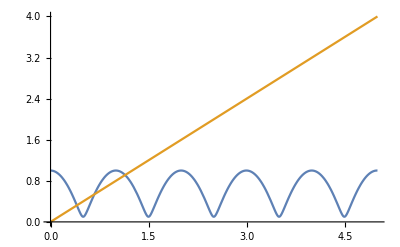

```mathematica
values={m->0.05,g->9.8,k->0.0493,R->0.5};
bc = {z[0]==1, z'[0]==0, phi[0]==0, phi'[0]==0.4/R};
sol1 = NDSolve[{eq1, eq2, bc (* equations and initial conditions *)}/.values,{z, phi},{t,0,5}];

Plot[{z[t]/.sol1, phi[t]/.sol1},{t,0,5}] (* replace "var1" with whatever generalized coordinate you defined; add any other plots necessary to show the evolution of each of your generalized coordinates. *)
```

Qualitative description of the motion:
The beads bounce back and forth between the maximum and minimum height (blue plot), and because there is initial angular velocity with no external torques effecting it the beat will also continuously wind around the cylinder (orange plot). 


Part F: If the particle is started at a certain special height and given no initial vertical velocity, it will always stay at that height. Determine that special height (symbolically first, then with the values given previously plugged in). Then solve the equations again using the new initial conditions that the particles starts at this special height and is flicked horizontally with a speed of 0.4 m/s. Plot the solution to verify that the height remains constant.

0.317194

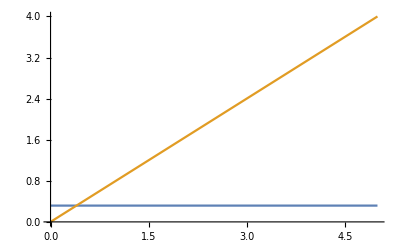

```mathematica
values={m->0.05,g->9.8,k->0.0493,R->0.5};
bc = {z[0]==Sqrt[k/(m*g)], z'[0]==0, phi[0]==0, phi'[0]==0.4/R};
sol1 = NDSolve[{eq1, eq2, bc }/.values,{z, phi},{t,0,5}];
Sqrt[k/(m*g)]/.values

Plot[{z[t]/.sol1, phi[t]/.sol1},{t,0,5}] (* replace "var1" with whatever generalized coordinate you defined; add any other plots necessary to show the evolution of each of your generalized coordinates. *)
```

Special height (symbolic answer): The height this is found is when the force of gravity equals the force of the air particles. i.e. mg = k/z^2. Assuming a positive heigh this occurs at Sqrt[ k/(m*g) ] meters.
Special height (numerical answer): 0.317194 meters